# Лабораторная 3

(вариант 10)

## Problem 1

```mathematica
(*парам сетки*)
```

```mathematica
Clear[y];
n=25;
tmax=1;
smax=20;
τ=N[tmax/smax];
l=1;
h=N[l/n];
σ=1;
uo[x_]=Sin[π*x];

Do [y[i,0]=uo[i h],{i,1,n-1}]
Do[y[0,s]=0;y[n,s]=0,{s,0,smax}]
eqn[s_]:=Table[(y[i,s+1]-y[i,s])/τ==(σ*((y[i+1,s+1]-2y[i,s+1]+y[i-1,s+1])/h^2))+((1-σ)*((y[i+1,s]-2y[i,s]+y[i-1,s])/h^2)),{i,1,n-1}]
Y[s_]:=Table[y[i,s],{i,1,n-1}]
Do[
{B,A}=CoefficientArrays [eqn[s],Y[s+1]];
yy = LinearSolve [A,-B];
Do[y[i,s+1]=yy[[i]],{i,1,n-1}]
,{s,0,smax-1}]
```

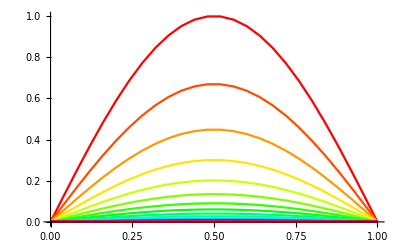

```mathematica
Show[Table[ListPlot[Table[{i h,y[i,s]},{i,0,n}],Joined->True,PlotStyle->Hue[s/smax]],{s,0,smax}]]
```

```mathematica
(*проверка точного решения*)
```

```mathematica
to[x_,t_]=Exp[-π^2 t]*Sin[π x];
k=1;
f1[x_,t_]=0;
D[to[x,t],t]==D[k*to[x,t],{x,2}]+f1[x,t]
```

True

```mathematica
(*зависимость от шага сетки h*)
```

```mathematica
τ=1/20;
tmax=1;
smax=tmax/τ;
l=1;
k=1;
σ=1;
dn=10;
Do [Clear[y];
Do[y[i,0]=uo[h i],{i,1,n-1}] 
Do[y[0,s]=0;y[n,s]=0,{s,0,smax}]
Do [{B,A}=CoefficientArrays[eqn[s], Y[s+1]];
yy = LinearSolve [A,-B];
Do[y[i,s+1]=yy[[i]],{i,1,n-1}]];
roor=Table[Abs[to[i h,τ s]-y[i,s]],{i,0,n},{i,0,n},{s,0,smax}];
eror=Max[roor];
eror1[k]=Table[eror,1];k++,{ n,10,dn}];
m=k;
eror2=Table[eror1[k],{k,1,m-1}];
ListPlot[Table[{(l/(k* dn)),eror2[[k,1]]},{k,1,m-1}],Joined->True,AxesLabel->{"h","err"},PlotRange->All]
```

Table::itform: Argument 1 at position 2 does not have the correct form for an iterator.

General::stop: Further output of Table :: itform will be suppressed during this calculation.

```mathematica
(*зависимость от параметра схемы σ*)
τ=1/20;
tmax=1;
smax=tmax/τ;
l=1;
n=20;
k=1;
h=N[l/n];
σ=1;
Clear[y];
dσ=0.1;
Do [Clear[y];
Do[y[i,0]=uo[h i],{i,1,n-1}] 
Do[y[0,s]=0;y[n,s]=0,{s,0,smax}]
For[s=0,s<smax,s++,{B,A}=CoefficientArrays[eqn[s],Y[s+1]];
yy = LinearSolve [A,-B];
Do[y[i,s+1]=yy[[i]],{i,1,n-1}];
roor=Table[Abs[to[i h,τ s]-y[i,s]],{i,0,n},{s,0,smax}]];
eror=Max[roor];
eror1[k]=Table[eror[k],{n,0,1}]];
p=k;
eror2=Table[eror1[k],{k,1,p-1}];
ListPlot[Table[{(l/(k dσ)),eror2[[k,1]]},{k,1,p-1}],Joined->True,AxesLabel->{"h","err"},PlotRange->All]
```

ListPlot::lpn: {{}} is not a list of numbers or pairs of numbers.

ListPlot[{},Joined→True,AxesLabel→{h,err},PlotRange→All]

## Problem 2

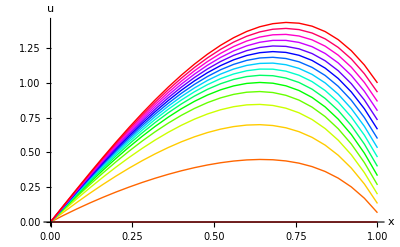

```mathematica
n=25;
tmax=1;
smax=15;
τ=N[tmax/smax];
l=1;
h=N[l/n];
σ=1;
κ[x_]=2-x;
f1[x_,t_]=10*(1+Tan[x-0.5]);
Clear[y1];
u0[x_]:=0;
Do [y1[i,0]=u0[i h],{i,1,n-1}] 
Do[y1[0,s]=0; y1[n,s]=s τ, {s,0,smax}]
eqn1[s_]:= Table[(y1[i,s+1]-y1[i,s])/τ==σ (κ[(i+1/2) h]1/h^2(y1[i+1,s+1]-y1[i,s+1])-κ[(i-1/2) h]1/h^2(y1[i,s+1]-y1[i-1,s+1]))+(1-σ)(κ[(i+1/2) h]1/h^2(y1[i+1,s+1]-y1[i,s+1])-κ[(i-1/2) h]1/h^2(y1[i,s+1]-y1[i-1,s+1]))+f1[i h,τ s], {i,1,n-1}]
Y1[s_]:=Table[y1[i,s],{i,1,n-1}];
Do [
{B,A}=CoefficientArrays[eqn1[s], Y1[s+1]];yy1 = LinearSolve [A,-B];Do[y1[i,s+1]=yy1[[i]],{i,1,n-1}],
{s,0,smax-1}]
Show[Table[ListPlot[Table[{i h, y1[i,s]},{i,0,n}], Joined-> True, PlotStyle->Hue[s/smax]],{s,0,smax}],PlotRange->Automatic,AxesLabel->{"x","u"}]
```